# Calculating AVS Curves

## QEA Boats Module

By Dieter Brehm & Sam Sam Daitzman

## Explanation

### This file contains Mathematica code for calculating the RM curve of a differently shaped three dimensional boats. First, we define our desired boats. Then, we define a function for finding the moment at a given heal angle. Finally, we map that function to several angles and generate a plot.

## Code

Defining and showing a plot of the two boats

```mathematica
(*boat = ImplicitRegion[(x)^2/(10.16)^2+(y-7.62)^2/(7.62)^2 +z^2/(20.32)^2<1 && y < 7.62,{ {x,-20,20},{y,-20,20},{z,-50,50}}];*)
boat = ImplicitRegion[(x)^2/(11.25)^2+(y-10.24)^2/(13.24)^2 +z^2/(20)^2<1 && 0<y < 11.24,{ {x,-20,20},{y,-20,20},{z,-50,50}}];
mast = ImplicitRegion[x^2+(z-0.9525)^2≤0.9525^2&&y≥0&&y≤50, {x,y,z}]
```

ImplicitRegion[x^2+(-0.9525+z)^2≤0.907256&&y≥0&&y≤50,{x,y,z}]

```mathematica
Show[
RegionPlot3D[boat, PlotTheme->"Web", AxesLabel->{"x(cm)","y(cm)","z(cm)"}, PlotPoints->55, PlotStyle->Directive[Yellow,Opacity[0.5]]]]
```

-Graphics3D-

```mathematica
Show[%42,ViewPoint->{∞,0,0}]
```

-Graphics3D-

```mathematica
Show[%42,ViewPoint->{0,0,∞}]
```

-Graphics3D-

```mathematica
Manipulate[RegionPlot[(x)^2/(11.25)^2+(y-10.24)^2/(13.24)^2 +(aa)^2/(20)^2<1 && 0<y < 11.24,{x,-20,20},{y,-20,20}],{aa,-19.8,19.8}]
```

Code for calculating moment of arbitrary ImplicitRegion boat at a heel angle

```mathematica
UnitConvert[Quantity[9.8, "Meters"/("Seconds")^2],"Centimeters"/("Seconds")^2]
```

980. cm/s^2

```mathematica
boatmass[boatregion_, density_] :=
 mass = N[(Volume[boatregion]*density)+700.,5]
boatcom[boatregion_, density_] := 
com = N[ 1/boatmass[DiscretizeRegion[boatregion], density]*NIntegrate[density*{x,y,z}, {x,y,z}∈DiscretizeRegion[boatregion]],5]
moment[hullshape_,mass_,com_,density_, theta_]:= Module[{},
rads = theta * (Pi/180);
water = ImplicitRegion[If[rads<Pi / 2,y<Tan[rads ]*x+d,y>Tan[rads ]*x+d],{ {x,-20,20},{y,-20,20},{z,-25,25}}];
under = RegionIntersection[hullshape, water];
disp = Integrate[1, {x,y,z}∈under];
draft = N[d/.FindRoot[disp==mass,{d,-20,20}][[1]]];
cob = RegionCentroid[under/.{d->draft}];
(* consider the mast as part of the equation*)
com[[2]] = ((mass * com[[2]])+(100*25))/(mass + 100);
(*Should the gravity here be 980 cm/s^2?*)
buoyancy = mass*980*{-Sin[rads],Cos[rads],0};
torque =Cross[cob-com, buoyancy][[3]];
torque
]
momentrender[hullshape_,mass_,com_,density_, theta_]:= Module[{},
rads = theta * (Pi/180);
(*TODO: add var for the draft offset due to moving the origin*)
water = ImplicitRegion[If[rads<Pi / 2,y<Tan[rads ]*x+15.24+d,y>Tan[rads ]*x+d],{ {x,-20,20},{y,-20,20},{z,-25,25}}];
under = RegionIntersection[hullshape, water];
(* we should define units globally or something, I forgot to change the density of water here earlier*)
disp = Integrate[1, {x,y,z}∈under];
draft = N[d/.FindRoot[disp==mass,{d,-20,20}][[1]]];
cob = RegionCentroid[under/.{d->draft}];
com[[2]] = ((mass * com[[2]])+(100*25))/(mass + 100);
buoyancy = (mass+100)*980*{-Sin[rads],Cos[rads],0};
torque =Cross[cob-com, buoyancy][[3]];
Print[StringForm["draft (cm): ``",N[draft,1]]];
Print[StringForm["Mass (g): ``",N[mass+100,1]]];
Print[StringForm["cob (cm): ``",N[cob,1]]];
Print[StringForm["com (cm): ``",N[com,1]]];
Print[StringForm["Buoyancy Force (g/cm/s^2): ``",N[buoyancy,1]]];
Print[StringForm["Gravitational Force (g/cm/s^2): ``",N[mass*980,1]]];
Print[StringForm["Net Torque (g/cm^2/s^2): ``",N[(mass+100)*980,1]]];
Print[Show[
RegionPlot3D[boat, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->55, PlotStyle->Directive[Yellow,Opacity[0.2]]],
RegionPlot3D[water/.{d->draft}, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->55, PlotStyle->Directive[Blue,Opacity[0.3]]],
RegionPlot3D[under/.{d->draft}, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->55, PlotStyle->Directive[Blue,Opacity[0.2]]],RegionPlot3D[mast, PlotTheme->"Web", AxesLabel->{"x(cm)","y(cm)","z(cm)"}, PlotPoints->55, PlotStyle->Directive[Yellow,Opacity[0.2]]],
ListPointPlot3D[{com}, PlotStyle->Directive[Cyan,Opacity[1]]],
ListPointPlot3D[{cob}, PlotStyle->Directive[Red,Opacity[1]]],
ListPointPlot3D[{{0,25,0}}, PlotStyle->Directive[Red,Opacity[1]]]
]]
]
```

```mathematica
findAVS[boat_, density_]:=(
a={};
b = {1,21,41,61,81,101,121,141,161};
For[i=1,i<180,i+=20, Print[i];a =Append[a,Quiet[moment[boat,boatmass[boat, N[density,1]],boatcom[boat,N[density,1]],N[density,1],N[i,1]]]]];
data=Transpose@{b,a};
boatfunction=Interpolation[data];
Values@FindRoot[boatfunction[x]==0,{x,100}])[[1]]
plotAVS[boat_, density_]:=(
a={};
b = {1,21,41,61,81,101,121,141,161};
For[i=1,i<180,i+=20, Print[i];a =Append[a,Quiet[moment[boat,boatmass[boat, N[density,1]],boatcom[boat,N[density,1]],N[density,1],N[i,1]]]]];
data=Transpose@{b,a};
boatfunction=Interpolation[data];
Print[Show[
ListPlot[data],Plot[boatfunction[x],{x,0,180}]]];
Values@FindRoot[boatfunction[x]==0,{x,100}])[[1]]
```

```mathematica
boatmass[boat,N[0.01]]
boatcom[boat,N[0.01]]
```

1047.59

{3.58863×10^-6,0.269909,-8.42422×10^-6}

1

21

41

61

81

101

121

141

161

InterpolatingFunction::dmval: Input value {0.00367714} lies outside the range of data in the interpolating function. Extrapolation will be used.

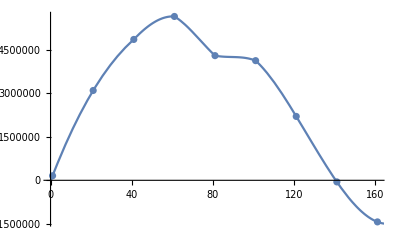

InterpolatingFunction::dmval: Input value {274.43} lies outside the range of data in the interpolating function. Extrapolation will be used.

140.455

```mathematica
avsangle = plotAVS[boat, 0.01]
```

```mathematica
momentrender[boat,boatmass[boat, N[0.1,1]],boatcom[boat,N[0.1,1]],N[0.1,1],N[30,1]]
```

Set::setps: {0.0000254826,1.91661,-0.0000598198} in the part assignment is not a symbol.

draft (cm): -11.524

Mass (g): 1575.94

cob (cm): {3.66881,3.52157,-3.82538×10^-16}

com (cm): {0.0000254826,1.91661,-0.0000598198}

Buoyancy Force (g/cm/s^2): {-772211.,1.33751×10^6,0.}

Gravitational Force (g/cm/s^2): 1.44642×10^6

Net Torque (g/cm^2/s^2): 1.54442×10^6

-Graphics3D-